```mathematica
2-2
```

0

# Generalizations of the Nest Command

Nicholas Wheeler
29 December 2011

### Introduction

I have used these commands

```mathematica
Nest[f,x,4]
```

f[f[f[f[x]]]]

```mathematica
NestList[f,x,4]//TableForm
```

x
f[x]
f[f[x]]
f[f[f[x]]]
f[f[f[f[x]]]]

in some recent work involving random walksw on rectangular grids. But random walks on hexagonal grids ("graphene") have the property that the step-options alternate; the patterns is ABABABABA instead AAAAAAAAA. This circumstance motivates me to looks for a generalization of the nest command that produces composite functions of the form

```mathematica
f[g[f[g[f[x]]]]]
```

and, more generally,

```mathematica
Subscript[f, 5][Subscript[f, 4][Subscript[f, 3][Subscript[f, 2][Subscript[f, 1][x]]]]]
```

This problem—the problem of producing such constructs automatically/efficiently—gave me so much difficulty that I was motivated to write for advice to Patrick T. Tam, author of "A Physicist's Guide to Mathematica" [I wrote on the 23rd, have as yet received no reply]. Here I describe several elementary solutions or the problem thus posed.

### Constructing composite functions

```mathematica
?Composition
```

Composition[f_1,f_2,f_3,…] represents a composition of the functions f_1, f_2, f_3, … .

The problem here is that when the f_k are produced by some tabulated set of definitions they are enclosed in a collective {   }, and so long as those remain in place the Composition command does not work:

```mathematica
Table[Subscript[f, k],{k,1,10}]
```

{f_1,f_2,f_3,f_4,f_5,f_6,f_7,f_8,f_9,f_10}

```mathematica
Composition[{Subscript[f, 1],Subscript[f, 2],Subscript[f, 3],Subscript[f, 4],Subscript[f, 5],Subscript[f, 6],Subscript[f, 7],Subscript[f, 8],Subscript[f, 9],Subscript[f, 10]}][x]
```

{f_1,f_2,f_3,f_4,f_5,f_6,f_7,f_8,f_9,f_10}[x]

I know of no command that serves to remove the offending brackets. By-hand removal works

```mathematica
Composition[Subscript[f, 1],Subscript[f, 2],Subscript[f, 3],Subscript[f, 4],Subscript[f, 5],Subscript[f, 6],Subscript[f, 7],Subscript[f, 8],Subscript[f, 9],Subscript[f, 10]][x]
```

f_1[f_2[f_3[f_4[f_5[f_6[f_7[f_8[f_9[f_10[x]]]]]]]]]]

but is a procedure that becomes unworkable when Composition is folded into a compound command. Even more awkward in such contexts is the construction

```mathematica
Subscript[f, 1]@Subscript[f, 2]@Subscript[f, 3]@Subscript[f, 4]@Subscript[f, 5][x]
```

f_1[f_2[f_3[f_4[f_5[x]]]]]

The command

```mathematica
?ComposeList
```

ComposeList[{f_1,f_2,…},x] generates a list of the form {x,f_1[x],f_2[f_1[x]],…}.

releases one from the bracket problem. It produces

```mathematica
ComposeList[{Subscript[f, 1],Subscript[f, 2],Subscript[f, 3],Subscript[f, 4],Subscript[f, 5],Subscript[f, 6],Subscript[f, 7],Subscript[f, 8],Subscript[f, 9],Subscript[f, 10]},x]//TableForm
```

x
f_1[x]
f_2[f_1[x]]
f_3[f_2[f_1[x]]]
f_4[f_3[f_2[f_1[x]]]]
f_5[f_4[f_3[f_2[f_1[x]]]]]
f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]
f_7[f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]]
f_8[f_7[f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]]]
f_9[f_8[f_7[f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]]]]
f_10[f_9[f_8[f_7[f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]]]]]

whence

```mathematica
ComposeList[{Subscript[f, 1],Subscript[f, 2],Subscript[f, 3],Subscript[f, 4],Subscript[f, 5],Subscript[f, 6],Subscript[f, 7],Subscript[f, 8],Subscript[f, 9],Subscript[f, 10]},x]//Last
```

f_10[f_9[f_8[f_7[f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]]]]]

I describe now a home-grown alternative procedure for constructing that result

```mathematica
F[n_]:=Subscript[f, n]@F[n-1];F[0]=x;
```

```mathematica
F[10]
```

f_10[f_9[f_8[f_7[f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]]]]]

and this duplication of the effect of ComposeList:

```mathematica
Table[F[k],{k,1,10}]//TableForm
```

f_1[x]
f_2[f_1[x]]
f_3[f_2[f_1[x]]]
f_4[f_3[f_2[f_1[x]]]]
f_5[f_4[f_3[f_2[f_1[x]]]]]
f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]
f_7[f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]]
f_8[f_7[f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]]]
f_9[f_8[f_7[f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]]]]
f_10[f_9[f_8[f_7[f_6[f_5[f_4[f_3[f_2[f_1[x]]]]]]]]]]

### Additive composite functions

I take my motivation from the circumstance that random walks evolve by step-wise addition. I look first to the efficient construction of

#### Scalar iterative sequences

of the form

```mathematica
x
%+Subscript[a, 1]
%+Subscript[a, 2]
%+Subscript[a, 3]
```

x

x+a_1

x+a_1+a_2

x+a_1+a_2+a_3

The following command produces a funny-looking result

```mathematica
F[k_]:=Function[u,u+Subscript[a, k]]
F[k]
```

Function[u$,u$+a_k]

but when applied to an argument [x] is seen to produce results of the desired form

```mathematica
F[1][x]
F[2][x]
F[3][x]
```

x+a_1

x+a_2

x+a_3

and it is seen moreover to compose well:

```mathematica
x
F[1][x]
F[2][%]
F[3][%]
F[4][%]
```

x

x+a_1

x+a_1+a_2

x+a_1+a_2+a_3

x+a_1+a_2+a_3+a_4

To automate that construction, we command

```mathematica
ℱ=Table[F[k],{k,1,5}];
ComposeList[ℱ,x]//TableForm
```

x
x+a_1
x+a_1+a_2
x+a_1+a_2+a_3
x+a_1+a_2+a_3+a_4
x+a_1+a_2+a_3+a_4+a_5

To construct such sequences that begin at the origin we command

```mathematica
ComposeList[ℱ,0]//TableForm
```

0
a_1
a_1+a_2
a_1+a_2+a_3
a_1+a_2+a_3+a_4
a_1+a_2+a_3+a_4+a_5

We have interest ultimately in walks with site-specific next-step probabilities, so look to this generalization of the preceding construction:

```mathematica
Clear[F]
F[k_]:=Function[u,u+Subscript[a, k][u]]
F[k]
```

Function[u$,u$+a_k[u$]]

```mathematica
x
F[1][x]
F[2][%]
F[3][%]
F[4][%]
```

x

x+a_1[x]

x+a_1[x]+a_2[x+a_1[x]]

x+a_1[x]+a_2[x+a_1[x]]+a_3[x+a_1[x]+a_2[x+a_1[x]]]

x+a_1[x]+a_2[x+a_1[x]]+a_3[x+a_1[x]+a_2[x+a_1[x]]]+a_4[x+a_1[x]+a_2[x+a_1[x]]+a_3[x+a_1[x]+a_2[x+a_1[x]]]]

```mathematica
Clear[ℱ]
ℱ=Table[F[k],{k,1,4}];
ComposeList[ℱ,x]//TableForm
```

x
x+a_1[x]
x+a_1[x]+a_2[x+a_1[x]]
x+a_1[x]+a_2[x+a_1[x]]+a_3[x+a_1[x]+a_2[x+a_1[x]]]
x+a_1[x]+a_2[x+a_1[x]]+a_3[x+a_1[x]+a_2[x+a_1[x]]]+a_4[x+a_1[x]+a_2[x+a_1[x]]+a_3[x+a_1[x]+a_2[x+a_1[x]]]]

```mathematica
ComposeList[ℱ,x]//Last
```

x+a_1[x]+a_2[x+a_1[x]]+a_3[x+a_1[x]+a_2[x+a_1[x]]]+a_4[x+a_1[x]+a_2[x+a_1[x]]+a_3[x+a_1[x]+a_2[x+a_1[x]]]]

```mathematica
ComposeList[ℱ,0]//TableForm
```

0
a_1[0]
a_1[0]+a_2[a_1[0]]
a_1[0]+a_2[a_1[0]]+a_3[a_1[0]+a_2[a_1[0]]]
a_1[0]+a_2[a_1[0]]+a_3[a_1[0]+a_2[a_1[0]]]+a_4[a_1[0]+a_2[a_1[0]]+a_3[a_1[0]+a_2[a_1[0]]]]

Walks on the plane (or on 2-dimensional lattices) require x and the constants a_k to be 2-vectors, so I look next to

#### 2-vector-valued iterative sequences

The construction

```mathematica
F2[k_]:=Function[{Subscript[a, k]+#1,Subscript[b, k]+#2}]
F2[1][x,y]
```

{x+a_1,y+b_1}

and its generalized counterpart

```mathematica
G2[k_]:=Function[{Subscript[a, k][#1,#2]+#1,Subscript[b, k][#1,#2]+#2}]
G2[1][x,y]
```

{x+a_1[x,y],y+b_1[x,y]}

work well enough on first application, but they fail to iterate; they wrap their output in braces {  }. Iteration requires, however, that those be removed (replaced by [  ]). Here I do so by hand, and get the anticipated result:

```mathematica
G2[2][x+Subscript[a, 1][x,y],y+Subscript[b, 1][x,y]]
%//TableForm
```

{x+a_1[x,y]+a_2[x+a_1[x,y],y+b_1[x,y]],y+b_1[x,y]+b_2[x+a_1[x,y],y+b_1[x,y]]}

x+a_1[x,y]+a_2[x+a_1[x,y],y+b_1[x,y]]
y+b_1[x,y]+b_2[x+a_1[x,y],y+b_1[x,y]]

I know of no standard way to convert

{x,y}⟶[x,y]

but have produced a clumsy work-around, which hinges on the circumstance that

```mathematica
?Apply
```

Apply[f,expr] or f@@expr replaces the head of expr by f. 
Apply[f,expr,levelspec] replaces heads in parts of expr specified by levelspec.

"gets rid of a level of lists", which Mathematica illustrates (in full form and shorthand) as follows:

```mathematica
Apply[f,{{a,b},{c},d}]
f@@{{a,b},{c},d}
```

f[{a,b},{c},d]

f[{a,b},{c},d]

Define

```mathematica
s[k_]:=Function[{Subscript[a, k]+#1,Subscript[b, k]+#2}]
```

and the iterative procedure

```mathematica
S[n_]:=Apply[s[n],S[n-1]]
```

Then get

```mathematica
S[0]={x,y}
S[1]
```

{x,y}

{x+a_1,y+b_1}

with this automated continuation:

```mathematica
Table[S[k],{k,1,4}]//TableForm
```

x+a_1 | y+b_1
x+a_1+a_2 | y+b_1+b_2
x+a_1+a_2+a_3 | y+b_1+b_2+b_3
x+a_1+a_2+a_3+a_4 | y+b_1+b_2+b_3+b_4

```mathematica
S[10]
```

{x+a_1+a_2+a_3+a_4+a_5+a_6+a_7+a_8+a_9+a_10,y+b_1+b_2+b_3+b_4+b_5+b_6+b_7+b_8+b_9+b_10}

Having in mind walks with site-specific next-step probabilities, I construct

```mathematica
t[k_]:=Function[{Subscript[a, k][#1,#2]+#1,Subscript[b, k][#1,#2]+#2}]
T[n_]:=Apply[t[n],T[n-1]]
```

```mathematica
T[0]={x,y}
T[1]
T[2]//TableForm
T[3]//TableForm
```

{x,y}

{x+a_1[x,y],y+b_1[x,y]}

x+a_1[x,y]+a_2[x+a_1[x,y],y+b_1[x,y]]
y+b_1[x,y]+b_2[x+a_1[x,y],y+b_1[x,y]]

x+a_1[x,y]+a_2[x+a_1[x,y],y+b_1[x,y]]+a_3[x+a_1[x,y]+a_2[x+a_1[x,y],y+b_1[x,y]],y+b_1[x,y]+b_2[x+a_1[x,y],y+b_1[x,y]]]
y+b_1[x,y]+b_2[x+a_1[x,y],y+b_1[x,y]]+b_3[x+a_1[x,y]+a_2[x+a_1[x,y],y+b_1[x,y]],y+b_1[x,y]+b_2[x+a_1[x,y],y+b_1[x,y]]]

REMARK: I wasted several days in an effort to get

Nest
NestList
Composition
ComposeList

to produce these results, the problem being in every case that I encountered brackets {  } where I wanted brackets [  ].

### Application: unweighted random walks on graphene

Familiarly, we confront now (see "Hexagonal Walks," 1 December 2011) a situation in which the walker stands on nodes of alternating color ●→●→●→●→●

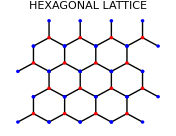

and whose next-step options are of alternating types:

```mathematica
-Graphics--Graphics-
```

Assuming all lattice edges (steps) to have unit length, the Red/Blue step-vectors are

```mathematica
R1=N[{Cos[π/2],Sin[π/2]}];
R2=N[{Cos[π/2-4(2π)/12],Sin[π/2-4(2π)/12]}];
R3=N[{Cos[π/2-8(2π)/12],Sin[π/2-8(2π)/12]}];
B1=-R1;
B2=-R2;
B3=-R3;
```

```mathematica
{Norm[R1],Norm[R2],Norm[R3]}
```

{1.,1.,1.}

It is to speed up subsequent computations that I have presented those vectors in such a way that their components are decimal reals, rather than algebraic constructs;  compare the following:

```mathematica
{Cos[π/2-4(2π)/12],Sin[π/2-4(2π)/12]}
R2
```

{(√3)/2,-1/2}

{0.866025,-0.5}

Be direct appropriation of the argument developed in "Hexagonal Walks," I construct a random population of 200 alternated RB steps

```mathematica
A200 = Table[Transpose[{{RandomChoice[{R1, R2, R3}], RandomChoice[{B1, B2, B3}]}}], {k, 1, 200}];

B200=Table[MatrixPower[({{0, 1}, {1, 0}}),k].A200⟦k⟧,{k,1,200}];
Steps200=Prepend[Table[B200⟦k⟧⟦1⟧⟦1⟧,{k,1,200}],{0,0}];
```

Here follow a few commands that tell us how many steps we have constructed

```mathematica
Length[Steps200]
```

201

and what a few of them look like:

```mathematica
Steps200⟦1;;4⟧
```

{{0,0},{-0.866025,0.5},{-0.866025,-0.5},{0.866025,0.5}}

```mathematica
Steps200//First
Steps200//Last
```

{0,0}

{0.866025,-0.5}

Here I use that data to check out the commands that will extract the x and y-components of those vectors:

```mathematica
Steps200⟦201⟧⟦1⟧
Steps200⟦201⟧⟦2⟧
```

0.866025

-0.5

It is at this point that we depart from the procedure spelled out in "Hexagonal Walks", in this specific regard: we use a recursive construction to replace the use made in "Hexagonal Walks" of the ∑_(j  =1)^k . Define

```mathematica
Table[{Subscript[a, k]=Steps200⟦k⟧⟦1⟧,Subscript[b, k]=Steps200⟦k⟧⟦2⟧},{k,1,201}];
```

which produces results like these:

```mathematica
Subscript[a, 201]
Subscript[b, 201]
```

0.866025

-0.5

Those are the {a, b} values that will at this point be fed into  the construction of the iterated function S[k] :

```mathematica
{x,y}={0,0}
Table[S[k],{k,1,4}]
```

{0,0}

{{0,0},{-0.866025,0.5},{-1.73205,0.},{-0.866025,0.5}}

The functions S[k] now describe a 201-step hexagonal walk that begins and ends at these points:

```mathematica
S[1]
S[201]
```

{0,0}

{0.866025,4.5}

Finally we plot that walk:

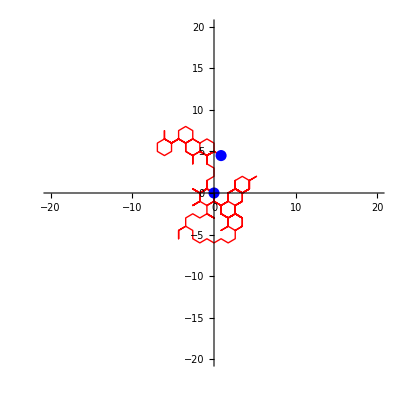

```mathematica
HexagonalWalk200=ListLinePlot[Table[S[k],{k,1,201}],AspectRatio->Automatic, AxesOrigin->{0,0}, PlotRange->{{-20,20},{-20,20}}, PlotStyle->{Thick, Red}];
EndPoints200=Graphics[{{Blue, PointSize[0.02],Point[S[1]]},
{Blue, PointSize[0.02],Point[S[201]]}}];
Show[{HexagonalWalk200,EndPoints200}]
```

I consolidate those commands, modified now so as to produce 250-step walks with a single ⌤. 

REMARK: I found while preparing this command that, when I tried similarly to produce 300-step walks, Mathematica complained that "the RecursionLimit has been exceeded." I think I had hit upon a machine limitation; when changed all 300s and 301s to 250s and 251s everything progressed as smoothly (and almost as quickly) as it did the previous 200-step walks. The execution time on my iMac is about 2 seconds.

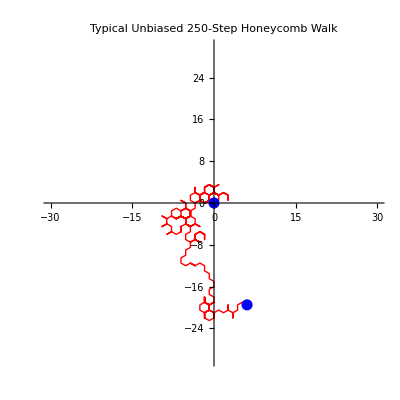

```mathematica
A250 = Table[Transpose[{{RandomChoice[{R1, R2, R3}], RandomChoice[{B1, B2, B3}]}}], {k, 1, 250}];

B250=Table[MatrixPower[({{0, 1}, {1, 0}}),k].A250⟦k⟧,{k,1,250}];
Steps250=Prepend[Table[B250⟦k⟧⟦1⟧⟦1⟧,{k,1,250}],{0,0}];

Table[{Subscript[a, k]=Steps250⟦k⟧⟦1⟧,Subscript[b, k]=Steps250⟦k⟧⟦2⟧},{k,1,251}];

{x,y}={0,0};

HexagonalWalk250=ListLinePlot[Table[S[k],{k,1,251}],AspectRatio->Automatic, AxesOrigin->{0,0}, PlotRange->{{-30,30},{-30,30}}, PlotStyle->{Thick, Red}];
EndPoints250=Graphics[{{Blue, PointSize[0.02],Point[S[1]]},
{Blue, PointSize[0.02],Point[S[251]]}}];
Show[{HexagonalWalk250,EndPoints250},PlotLabel->"Typical Unbiased 250-Step Honeycomb Walk"]
```

REMARK: I encountered occasional 250-step walks that encountered a boundary of
a 20 × 20 display. I have never encountered the a boundary of this 30 × 30 display, though it is theoretically possible to achieve

```mathematica
Subscript[x250, max]=250Cos[π/12]//N
Subscript[y250, max]=125(1+Sin[π/12])//N
```

241.481

157.352

### Preliminary remarks concerning the distribution of endpoints

We expect the endpoints of N-step random walks on a honycomb, as on a grid with square tiles or the unarticulated plane, to be normally distributed,  with standard deviation proportional to N.

```mathematica
Hyperlink["Random Walks","http://en.wikipedia.org/wiki/Random_walk"]
```

We are in position now to demonstrate the point by Monte Carlo calculation: look to the endpoints of (say) 10,000 N-step honeycomb walks, increment N, then repeat the exercise. Etc. This, however, would be a very labor-intensive way to obtain approximate support of a theoretically anticipated result. 

A better way (less labor-intensive?) to obtain that information would be to (1) construct a hexagonal graph so large that it would be impossible for an N-step walker—departing from the origin—to reach a boudary of the graph, (2) build the site-specific step-probatilities into the design of correspondingly large Markov matrix 𝕄, and (3) look to the evolving stochastic vector

MatrixPower[𝕄,n].p_0

where p_0 describes known initial placement at the origin. But we confront at this point a nest of challenging technical problems:

1) How most naturally to associated (say) 1000 nodes in hexagonal array with the elements of a stochastic vector

```mathematica
Subscript[P, 0]=Subscript[({{Subscript[p, 1]}, {Subscript[p, 2]}, {Subscript[p, 3]}, {⋮}, {Subscript[p, 1000]}}), 0]
```

2) That done, how to construct the 1000 × 1000 adjacency matrix?

3) How to feed in the site-specific weights that enter into construction of the unbalanced matrix 𝕄?

4) How to display P_N as a density map on the hexagonal grid (which lives on the xy-plane)?

But so long as we restrict our attention (as above) to individual hexagonal walks we can avoid the full force of those problems, since such walks live on the tesselated xy-plane.

### Construction of site-specific next-step probabilities

#### Preparatory remarks

In the unbiased hexagonal walks I at each step used RandomChoice to instruct the walker which of three equally-weighted next-step options to select. But RancomChoice is capable also of making arbitrarily weighted choices:

```mathematica
?RandomChoice
```

RandomChoice[{e_1,e_2,…}] gives a pseudorandom choice of one of the e_i. 
RandomChoice[list,n] gives a list of n pseudorandom choices. 
RandomChoice[list,{n_1,n_2,…}] gives an n_1×n_2×…  array of pseudorandom choices. 
RandomChoice[{w_1,w_2,…}->{e_1,e_2,…}] gives a pseudorandom choice weighted by the w_i. 
RandomChoice[wlist->elist,n] gives a list of n weighted choices.
RandomChoice[wlist->elist,{n_1,n_2,…}] gives an n_1×n_2×… array of weighted choices.

as I demonstrate. Construct a triple of weights (elements of a 3-dimensional stochatic vector)

```mathematica
V=RandomInteger[{1,9},{1,3}]⟦1⟧;
W=V/Total[V];
Table[Subscript[w, k]=W⟦k⟧,{k,1,3}]
```

{1/3,7/24,3/8}

```mathematica
Total[%]
```

1

Our objective is to select ℝ with probability (or "weight") w_1, 𝕊 with weight w_2, 𝕋 with weight w_3.  To that end, command

```mathematica
RandomChoice[{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]}->{ℝ, 𝕊, 𝕋}]
```

𝕋

A short series of such commands produces

```mathematica
Table[RandomChoice[{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]}->{ℝ, 𝕊, 𝕋}],{k,1,100}]
```

{𝕊,ℝ,𝕊,ℝ,𝕊,𝕋,𝕋,ℝ,ℝ,ℝ,𝕋,ℝ,𝕊,ℝ,ℝ,ℝ,ℝ,𝕊,𝕋,ℝ,𝕊,𝕋,𝕊,ℝ,𝕋,𝕋,𝕊,𝕊,𝕋,ℝ,𝕋,ℝ,𝕋,ℝ,𝕊,𝕋,𝕋,ℝ,𝕋,ℝ,ℝ,𝕋,𝕊,𝕋,ℝ,𝕊,𝕋,ℝ,ℝ,ℝ,ℝ,ℝ,𝕊,𝕊,𝕊,ℝ,𝕊,ℝ,ℝ,𝕊,ℝ,ℝ,ℝ,ℝ,ℝ,ℝ,𝕋,𝕋,ℝ,𝕋,𝕊,𝕋,ℝ,𝕊,ℝ,𝕋,𝕊,ℝ,𝕋,ℝ,ℝ,𝕋,ℝ,𝕊,ℝ,𝕊,ℝ,𝕋,𝕊,𝕋,𝕊,ℝ,𝕋,𝕊,𝕋,𝕋,ℝ,𝕋,𝕊,𝕊}

Here we construct a series long enough to support a plausible statistical test of the effectiveness of the command:

```mathematica
Table[RandomChoice[{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]}->{ℝ, 𝕊, 𝕋}],{k,1,5000}];
```

```mathematica
Tally[%]
```

{{ℝ,1677},{𝕊,1427},{𝕋,1896}}

```mathematica
{{Subscript[w, 1],1677/5000},{Subscript[w, 2],1427/5000},{Subscript[w, 3],1896/5000}}//N
```

{{0.333333,0.3354},{0.291667,0.2854},{0.375,0.3792}}

We see that ℝ, 𝕊 and 𝕋 occur with frequencies that differ by only about 1% from our expectations.

#### Unbalanced hexagonal walk with site-independent weights

I introduce a set of more vividly differentiated weights

```mathematica
{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]}={6/10,3/10,1/10}
```

{3/5,3/10,1/10}

```mathematica
N[%]
```

{0.6,0.3,0.1}

and use those to modify the composite command that generated the preceding figure (here the suffix UB signals "Uniformly Biased")

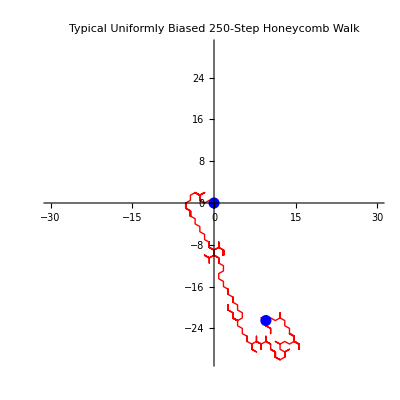

```mathematica
A250UB = Table[Transpose[{{RandomChoice[{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]}->{R1, R2, R3}], RandomChoice[{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]}->{B1, B2, B3}]}}], {k, 1, 250}];

B250UB=Table[MatrixPower[({{0, 1}, {1, 0}}),k].A250UB⟦k⟧,{k,1,250}];
Steps250UB=Prepend[Table[B250UB⟦k⟧⟦1⟧⟦1⟧,{k,1,250}],{0,0}];

Table[{Subscript[a, k]=Steps250UB⟦k⟧⟦1⟧,Subscript[b, k]=Steps250UB⟦k⟧⟦2⟧},{k,1,251}];

{x,y}={0,0};

HexagonalWalk250UB=ListLinePlot[Table[S[k],{k,1,251}],AspectRatio->Automatic, AxesOrigin->{0,0}, PlotRange->{{-30,30},{-30,30}}, PlotStyle->{Thick, Red}];
EndPoints250UB=Graphics[{{Blue, PointSize[0.02],Point[S[1]]},
{Blue, PointSize[0.02],Point[S[251]]}}];
Show[{HexagonalWalk250UB,EndPoints250UB},PlotLabel->"Typical Uniformly Biased 250-Step Honeycomb Walk"]
```

The characteristic design of the figures generated by that command can be understood as consequences of the fact that the figures that respresent "balanced next-step options"

```mathematica
-Graphics--Graphics-
```

have been replaced by the following:

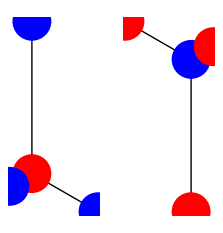

```mathematica
Subscript[R, 1]={Cos[π/2],Sin[π/2]};
Subscript[R, 2]={Cos[π/2-4(2π)/12],Sin[π/2-4(2π)/12]};
Subscript[R, 3]={Cos[π/2-8(2π)/12],Sin[π/2-8(2π)/12]};
WeightedRedSteps=Graphics[{{Red, PointSize[0.07],Point[{0,0}]},
{Blue, PointSize[0.07],Point[Subscript[w, 1] Subscript[R, 1]]},
{Blue, PointSize[0.07],Point[Subscript[w, 2] Subscript[R, 2]]},
{Blue, PointSize[0.07],Point[Subscript[w, 3] Subscript[R, 3]]},
{Arrow[{{0,0},Subscript[w, 1] Subscript[R, 1]},.01]},
{Arrow[{{0,0},Subscript[w, 2] Subscript[R, 2]},.0105]},
{Arrow[{{0,0},Subscript[w, 3] Subscript[R, 3]},.0105]}}];

Subscript[B, 1]=-Subscript[R, 1];
Subscript[B, 2]=-Subscript[R, 2];
Subscript[B, 3]=-Subscript[R, 3];
WeightedBlueSteps=Graphics[{{Blue, PointSize[0.07],Point[{0,0}]},
{Red, PointSize[0.07],Point[Subscript[w, 1] Subscript[B, 1]]},
{Red, PointSize[0.07],Point[Subscript[w, 2] Subscript[B, 2]]},
{Red, PointSize[0.07],Point[Subscript[w, 3] Subscript[B, 3]]},
{Arrow[{{0,0},Subscript[w, 1] Subscript[B, 1]},.01]},
{Arrow[{{0,0},Subscript[w, 2] Subscript[B, 2]},.0105]},
{Arrow[{{0,0},Subscript[w, 3] Subscript[B, 3]},.0105]}}];

GraphicsArray[{WeightedRedSteps,WeightedBlueSteps}]
```

REMARK: In the figure, length is used to indicate probability; actual step-length (unity) is the same in all cases.

#### Construction of site-specific weights

The motion executed by our walker is an idealized discontinuous motion to which the concepts of kinematics do not pertain; it cannot in any standard sense be said to possess a "velocity," and certainly not an "acceleration." Its motion is therefore not in any standard sense "dynamical," responsive to impressed "forces." The familiar dynamical resources—potential, Hamiltonian, Lagrangian—are therefore not available to serve as devices from which to extract evaluations of the site-specific weight factors

{w_1[x,y],w_2[x,y],w_3[x,y]}

REMARK: In "Letter to Patrick Tam 1" (22 December 2011) I describe a random walk on
2-dimensional phase space in which the oscillator Hamiltonian is used to control step-length, and randomness enters only into the decision whether the next step will be a δx-step or a
δp-step. The resulting walks look typically like these:

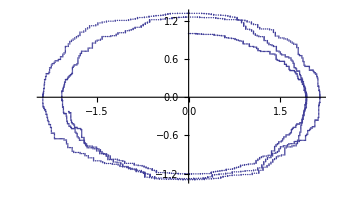

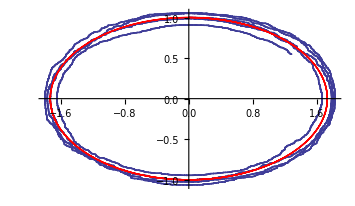

But lessons learned from that computational experience are irrelevant to the problem now at hand.

My initial intention had been to lay down a scalar field ϕ[x,y] and to use its directional derivatives to assign local value to {w_1,w_2,w_3}. I look by way of preparation to the problem of …

#### Directional derivative construction

For illustrative purposes, let

```mathematica
Clear[x,y,ϕ]
```

```mathematica
ϕ[x_,y_]:=1/(6π)(x^2+y^2)^3 ⅇ^(-(x^2+y^2))
```

This scalar field is rotationally symmetric; in polar coordinates it becomes

```mathematica
ϕ[r Cos[θ],r Sin[θ]]//Simplify
```

(ⅇ^(-r^2) r^6)/(6 π)

and I have—for no good reason—arrannged for it to be normalized:

```mathematica
Integrate[2π r (ⅇ^(-r^2) r^6)/(6 π),{r,0,∞}]
```

1

By design, it depends very simply on its arguments.

Here follow various graphic representations of ϕ :

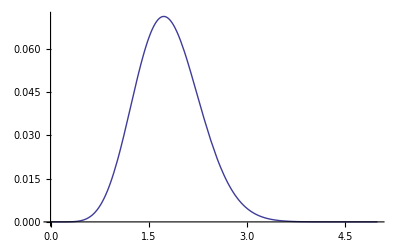

```mathematica
Plot[ (ⅇ^(-r^2) r^6)/(6 π),{r,0,5}]
```

```mathematica
Plot3D[ϕ[x,y],{x,-5,5},{y,-5,5}, Mesh->None, PlotPoints->70,PlotRange->{0,0.08},Boxed->False, Axes->False]
```

-Graphics3D-

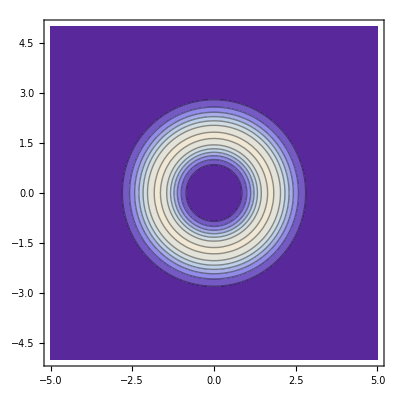

```mathematica
ContourPlot[ϕ[x,y],{x,-5,5},{y,-5,5}, PlotPoints->70]
```

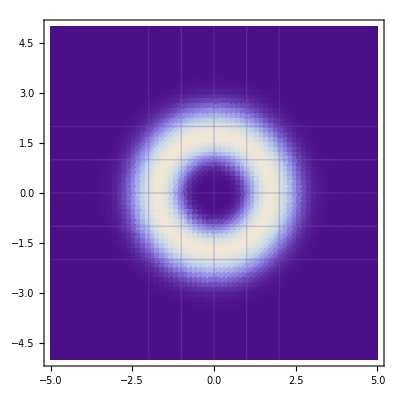

```mathematica
DensityPlot[ϕ[x,y],{x,-5,5},{y,-5,5}, PlotPoints->70,Mesh->9]
```

We propose to compute directional derivatives of ϕ in directions defined by six unit vectors

```mathematica
Table[Subscript[e, k]={Cos[-π/6+k π/3],Sin[-π/6+k π/3]},{k,1,6}]
```

{{(√3)/2,1/2},{0,1},{-(√3)/2,1/2},{-(√3)/2,-1/2},{0,-1},{(√3)/2,-1/2}}

which are deployed as shown in the following figure:

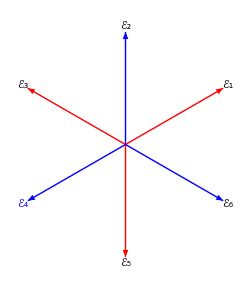

```mathematica
Graphics[{
{Red,Arrow[{{0,0},Subscript[e, 1]}]},
Text[Subscript[ℰ, 1],1.05 Subscript[e, 1]],
{Blue,Arrow[{{0,0},Subscript[e, 2]}]},
Text[Subscript[ℰ, 2],1.05 Subscript[e, 2]],
{Red,Arrow[{{0,0},Subscript[e, 3]}]},
Text[Subscript[ℰ, 3],1.05 Subscript[e, 3]],
{Blue,Arrow[{{0,0},Subscript[e, 4]}],
Text[Subscript[ℰ, 4],1.05 Subscript[e, 4]]},
{Red,Arrow[{{0,0},Subscript[e, 5]}]},
Text[Subscript[ℰ, 5],1.05 Subscript[e, 5]],
{Blue,Arrow[{{0,0},Subscript[e, 6]}]},
Text[Subscript[ℰ, 6],1.05 Subscript[e, 6]]}]
```

Working from

```mathematica
{D[ϕ[x,y], x],D[ϕ[x,y], y]}
```

{(ⅇ^(-x^2-y^2) x (x^2+y^2)^2)/π-(ⅇ^(-x^2-y^2) x (x^2+y^2)^3)/(3 π),(ⅇ^(-x^2-y^2) y (x^2+y^2)^2)/π-(ⅇ^(-x^2-y^2) y (x^2+y^2)^3)/(3 π)}

we obtain this description of grad ϕ

```mathematica
grad[x_,y_]:={(ⅇ^(-x^2-y^2) x (x^2+y^2)^2)/π-(ⅇ^(-x^2-y^2) x (x^2+y^2)^3)/(3 π),(ⅇ^(-x^2-y^2) y (x^2+y^2)^2)/π-(ⅇ^(-x^2-y^2) y (x^2+y^2)^3)/(3 π)}
```

which supplies results such as the following:

```mathematica
grad[1,1]
grad[1.,1.]
grad[1,0.5]
```

{4/(3 ⅇ^2 π),4/(3 ⅇ^2 π)}

{0.0574381,0.0574381}

{0.0831225,0.0415613}

Directional derivatives are constructs of the form

unitvector.grad

Making use now of the this constructin of the dot product

```mathematica
{a,b}.{c,d}
```

a c+b d

Here are the six directional derivatives at {x, y} = {1, 0.5}:

```mathematica
Table[Subscript[e, k].grad[1,0.5],{k,1,6}]
```

{0.0927669,0.0415613,-0.0512056,-0.0927669,-0.0415613,0.0512056}

Notice that three are the negatives of the other three. From

```mathematica
Manipulate[Table[Subscript[e, k].grad[x,y],{k,1,6}],{x,0,5},{y,0,5}]
```

we see that that state of affairs is entirely typical; it reflects simply the fact that three of our 
e-directions are opposites of the other three.

Let a "tile" be tangent at a regular point P to the ϕ-surface defined

z=ϕ[x,y]

Inscribe one or the other of the following figures

```mathematica
RedTile=Graphics[{
{Red,Arrow[{{0,0},Subscript[e, 1]}]},
Text[Subscript[ℰ, 1],1.05 Subscript[e, 1]],
{Red,Arrow[{{0,0},Subscript[e, 3]}]},
Text[Subscript[ℰ, 3],1.05 Subscript[e, 3]],
{Red,Arrow[{{0,0},Subscript[e, 5]}]},
Text[Subscript[ℰ, 5],1.05 Subscript[e, 5]]}];
```

```mathematica
BlueTile=Graphics[{
{Blue,Arrow[{{0,0},Subscript[e, 2]}]},
Text[Subscript[ℰ, 2],1.05 Subscript[e, 2]],
{Blue,Arrow[{{0,0},Subscript[e, 4]}],
Text[Subscript[ℰ, 4],1.05 Subscript[e, 4]]},
{Blue,Arrow[{{0,0},Subscript[e, 6]}]},
Text[Subscript[ℰ, 6],1.05 Subscript[e, 6]]}];
```

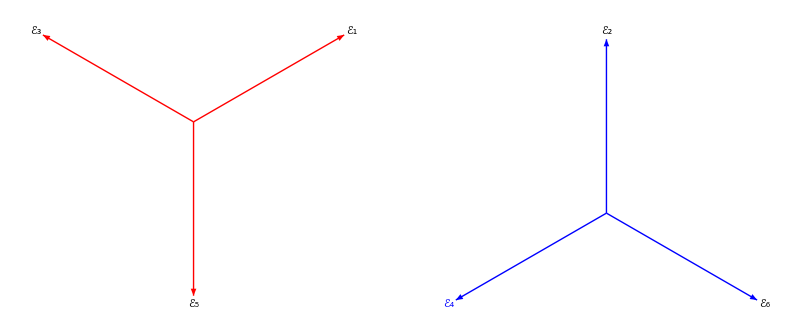

```mathematica
GraphicsArray[{RedTile, BlueTile}]
```

on the tile (origin at P, the point of tangency). It is clear that, however the figure is oriented (twirled about the point of tangency), at least one and not more than two of the arrows will have negative slope, the only exception arising when P marks a local minimum, maximum or a saddle point, where all arrows have zero slope.

The following figures fold that circumstance into the atypical circumstance that our ϕ happens to be rotationally symmetric :

```mathematica
Plot3D[Subscript[e, 1].grad[x,y],{x,-5,5},{y,-5,5},PlotRange->{-0.1,0.1},PlotPoints->50]
Plot3D[Subscript[e, 2].grad[x,y],{x,-5,5},{y,-5,5},PlotRange->{-0.1,0.1},PlotPoints->50]
Plot3D[Subscript[e, 3].grad[x,y],{x,-5,5},{y,-5,5},PlotRange->{-0.1,0.1},PlotPoints->50]
Plot3D[Subscript[e, 4].grad[x,y],{x,-5,5},{y,-5,5},PlotRange->{-0.1,0.1},PlotPoints->50]
Plot3D[Subscript[e, 5].grad[x,y],{x,-5,5},{y,-5,5},PlotRange->{-0.1,0.1},PlotPoints->50]
Plot3D[Subscript[e, 6].grad[x,y],{x,-5,5},{y,-5,5},PlotRange->{-0.1,0.1},PlotPoints->50]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

#### From directional derivatives to weights

Mathematica's weighted RandomChoice command accepts any set {n_1,n_2,n_3} of positive numbers as weights, in the sense that it automatically normalizes those numbers

```mathematica
{Subscript[w, 1],Subscript[w, 2],Subscript[w, 3]}={Subscript[n, 1]/(Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3]),Subscript[n, 2]/(Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3]),Subscript[n, 3]/(Subscript[n, 1]+Subscript[n, 2]+Subscript[n, 3])}
```

as I demonstrate:

```mathematica
Table[RandomChoice[{1,2,3}->{a,b,c}],{k,1,10000}];
```

```mathematica
Tally[%]
```

{{a,1659},{b,3378},{c,4963}}

We expect b to occur twice as often as a, and c to occur three times as often as a, and in fact we have

```mathematica
RatiobToa=Round[3378/1659]
RatiocToa=Round[4963/1659]
```

2

3

The weighted RandomChoice command fails, however, if either (1) any proposed weight is negative, or (2) the sum of the proposed weights is zero (rendering normalization impossible). 

An obvious way to deal with these circumstances is (1) to associate zero weight with all negative directional derivatives, and (2) to write

weight = directional derivative + small positive constant

whenever the directional derivative is ⩾  0. To that end, we construct

```mathematica
Subscript[f, 1][x_,y_]:=Which[Subscript[e, 1].grad[x,y]<0,0,Subscript[e, 1].grad[x,y]⩾0,0.001+Subscript[e, 1].grad[x,y]]

Subscript[f, 2][x_,y_]:=Which[Subscript[e, 2].grad[x,y]<0,0,Subscript[e, 2].grad[x,y]⩾0,0.001+Subscript[e, 2].grad[x,y]]

Subscript[f, 3][x_,y_]:=Which[Subscript[e, 3].grad[x,y]<0,0,Subscript[e, 3].grad[x,y]⩾0,0.001+Subscript[e, 3].grad[x,y]]

Subscript[f, 4][x_,y_]:=Which[Subscript[e, 4].grad[x,y]<0,0,Subscript[e, 4].grad[x,y]⩾0,0.001+Subscript[e, 4].grad[x,y]]

Subscript[f, 5][x_,y_]:=Which[Subscript[e, 5].grad[x,y]<0,0,Subscript[e, 5].grad[x,y]⩾0,0.001+Subscript[e, 5].grad[x,y]]

Subscript[f, 6][x_,y_]:=Which[Subscript[e, 6].grad[x,y]<0,0,Subscript[e, 6].grad[x,y]⩾0,0.001+Subscript[e, 6].grad[x,y]]
```

REMARK: One might alternatively employ these constructions

```mathematica
Subscript[g, 1][x_,y_]:=0.001+UnitStep[Subscript[e, 1].grad[x,y]]Subscript[e, 1].grad[x,y]
Subscript[g, 2][x_,y_]:=0.001+UnitStep[Subscript[e, 2].grad[x,y]]Subscript[e, 2].grad[x,y]
Subscript[g, 3][x_,y_]:=0.001+UnitStep[Subscript[e, 3].grad[x,y]]Subscript[e, 3].grad[x,y]
Subscript[g, 4][x_,y_]:=0.001+UnitStep[Subscript[e, 4].grad[x,y]]Subscript[e, 4].grad[x,y]
Subscript[g, 5][x_,y_]:=0.001+UnitStep[Subscript[e, 5].grad[x,y]]Subscript[e, 5].grad[x,y]
Subscript[g, 6][x_,y_]:=0.001+UnitStep[Subscript[e, 6].grad[x,y]]Subscript[e, 6].grad[x,y]
```

which are prettier, and are seen in this example

```mathematica
Subscript[f, 1][1,1]
Subscript[g, 1][1,1]
```

0.0794619

0.0794619

to work just as well. It remains to discover whether one is faster than the other, and whether the UnitStep discontinuity will sometimes pose a problem (of course, Which presents its own kind of discontinuity). As a speed test, I draw figures

```mathematica
Plot3D[Subscript[f, 1][x,y],{x,-5,5},{y,-5,5},PlotRange->{-0.1,0.1},PlotPoints->50]

Plot3D[Subscript[g, 1][x,y],{x,-5,5},{y,-5,5},PlotRange->{-0.1,0.1},PlotPoints->50]
```

-Graphics3D-

-Graphics3D-

and discover that both take about 4 seconds. But the latter draws white curves where the UnitStep discontinuity is encountered. So I elect to go with the functions f_i[x,y].

In support of a point made previously, range around on the 2D interval

{-5<x<+5,-5<y<+5}

```mathematica
Manipulate[{Subscript[f, 1][x,y],Subscript[f, 3][x,y],Subscript[f, 5][x,y]},{x,-5,5},{y,-5,5}]
```

and observe that always one and sometimes two (but never all) of the "chopped directional derivatives" {f_1,f_3,f_5} is zero (though at {x = 5, y = 5} we encounter {0, 0.001, 0.001} which would have been—in the displayed precision—{0, 0, 0} but for the additive 0.001 that was folded into the definitions of the f_i).

As a final demonstration of where we now stand, I construct (which takes about 5 seconds)

```mathematica
Table[RandomChoice[{Subscript[f, 1][1.53,-0.35],Subscript[f, 3][1.53,-0.35],Subscript[f, 5][1.53,-0.35]}->{a,b,c}],{k,1,10000}];
```

```mathematica
Tally[%]
```

{{a,7459},{c,2541}}

So a, b and c occurred in that sample with frequencies

```mathematica
Subscript[Freq, a]=7459/10000//N
Subscript[Freq, b]=0/10000//N
Subscript[Freq, c]=2541/10000//N
```

0.7459

0.

0.2541

wherreas the expected frequencies were

```mathematica
Subscript[ExpectedFreq, a]=0.0348309/(0.0348309+0+0.0112962)
Subscript[ExpectedFreq, b]=0/(0.0348309+0+0.0112962)
Subscript[ExpectedFreq, c]=0.0112962/(0.0348309+0+0.0112962)
```

0.755107

0

0.244893

### Construction of a site-specific hexagonal walk

#### Remarks concerning the physics of the problem

I took up this project in response to a brief conversation with Sina Zeytinoglu, who expressed interest in "random walks on corrugated graphine," but gave no indication of what he understood to be the physics of such processes or the source of his interest in them…which I find I am unable to guess.

I do not expect the electrical/conductivity of a wire to depend measureably upon the shape of the wire, do not expect the effective resistance of a 2D sheet of conductive material (copper, graphene) to depend measureably upon the non-flatness/corregation of that sheet…unless, possibly, the characteristic length of the deformation is so small as to be comparable to the lattice constant, so small that is to say as to modulate the interatomic bonds.

What am I to suppose is the physical embodiment of the "walker"? An electron, an "exiton" of some sort (spin?). I have no specific knowledge of the (random? stimulated?) migration of electrons/exitons on periodic structures, but suppose "hopping models" might come into play. I would not expect such hopping to occur at regularly spaced temporal intervals, but that is of no immediate concern: my effort has been to describe the geometry of trajectories, not how they develop in time.

Issues of computational/practical concern arise. The "corrugation length" must be enough larger than step-length for its effect to become evident as a modulation written upon the designs of random walks, yet not so large as to require walks so long that they saturate memory or take too long to compute.

In short: I feel—as a modeler—handicapped by the fact that I have no clear sense of the underlying physics of the processes I am attempting to model, no sharp intuitive sense of the results I expect to emerge. Sina spoke vaguely of "walks confined to channels," and it is for evidence of such (intuitively plausible) channeling that I will be looking…

…which informs the design of what I will now take to be my "scalar control field."

#### Corrugated control field

```mathematica
ψ[x_,y_]:=Sin[2π x/10]
```

```mathematica
Plot3D[ψ[x,y],{x,-20,20},{y,-20,20}]
```

-Graphics3D-

```mathematica
{D[ψ[x,y], x],D[ψ[x,y], y]}
```

{1/5 π Cos[(π x)/5],0}

```mathematica
gradψ[x_,y_]:={1/5 π Cos[(π x)/5],0}
```

```mathematica
Subscript[F, 1][x_,y_]:=Which[Subscript[e, 1].gradψ[x,y]<0,0,Subscript[e, 1].gradψ[x,y]⩾0,0.001+Subscript[e, 1].gradψ[x,y]]

Subscript[F, 2][x_,y_]:=Which[Subscript[e, 2].gradψ[x,y]<0,0,Subscript[e, 2].gradψ[x,y]⩾0,0.001+Subscript[e, 2].gradψ[x,y]]

Subscript[F, 3][x_,y_]:=Which[Subscript[e, 3].gradψ[x,y]<0,0,Subscript[e, 3].gradψ[x,y]⩾0,0.001+Subscript[e, 3].gradψ[x,y]]

Subscript[F, 4][x_,y_]:=Which[Subscript[e, 4].gradψ[x,y]<0,0,Subscript[e, 4].gradψ[x,y]⩾0,0.001+Subscript[e, 4].gradψ[x,y]]

Subscript[F, 5][x_,y_]:=Which[Subscript[e, 5].gradψ[x,y]<0,0,Subscript[e, 5].gradψ[x,y]⩾0,0.001+Subscript[e, 5].gradψ[x,y]]

Subscript[F, 6][x_,y_]:=Which[Subscript[e, 6].gradψ[x,y]<0,0,Subscript[e, 6].gradψ[x,y]⩾0,0.001+Subscript[e, 6].gradψ[x,y]]
```

```mathematica
Plot3D[Subscript[F, 1][x,y],{x,-20,20},{y,-20,20}]
Plot3D[Subscript[F, 2][x,y],{x,-20,20},{y,-20,20}]
Plot3D[Subscript[F, 3][x,y],{x,-20,20},{y,-20,20},PlotPoints->50]
Plot3D[Subscript[F, 4][x,y],{x,-20,20},{y,-20,20},PlotPoints->50]
Plot3D[Subscript[F, 5][x,y],{x,-20,20},{y,-20,20}]
Plot3D[Subscript[F, 6][x,y],{x,-20,20},{y,-20,20}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

```mathematica
Plot3D[Subscript[F, 2][x,y],{x,-20,20},{y,-20,20}]
```

-Graphics3D-

```mathematica
Manipulate[{Subscript[F, 1][x,y],Subscript[F, 3][x,y],Subscript[F, 5][x,y]},{x,-10,10},{y,-10,10}]

Manipulate[{Subscript[F, 2][x,y],Subscript[F, 4][x,y],Subscript[F, 6][x,y]},{x,-10,10},{y,-10,10}]
```